## Profit Function

```mathematica
(*Clear[Qp,Kmax,DeltaKad,lambda,ka,Qp,kQ]*)
```

```mathematica
constants={kPmax->5,DeltakP->4,lambda->1,ka->4,Qp->40,kQ->1,x ->13/25}
```

{kPmax→5,DeltakP→4,lambda→1,ka→4,Qp→40,kQ→1,x→13/25}

```mathematica
(* Set the Kpfree parameter. It kp responds to advertising. Currently using linear piecewise function. *)
Kfree[ai_,abar_]=Piecewise[{
{kPmax,ai-abar≤-lambda},
{kPmax-(DeltakP/(2*lambda)) (ai-abar)+DeltakP/2,-lambda<ai-abar≤lambda},{kPmax-DeltakP,ai-abar>lambda}
}];
Kfree[ai,abar]
```

Piecewise[{{kPmax, -abar+ai≤-lambda}, {DeltakP/2+kPmax-((-abar+ai) DeltakP)/(2 lambda), -lambda<-abar+ai≤lambda}, {-DeltakP+kPmax, -abar+ai>lambda}, {0, True}}]

```mathematica
(* Setting up the profit function. Need to find the optimal profit value. *)
(*Q := Qp- Kfree[ai,avg] * P ; (*Q is the demand*)*)
Q:= Qp-kP*P;
R := Q*P; (*R is the revenue*);
(*Print[R]*)
```

```mathematica
(* Assume linear costs for simplicity *)
Cost[Q_,ai_]:=kQ*Q+ka*ai;
Print[Cost[Q,ai]]
```

ai ka+kQ (-kP P+Qp)

```mathematica
(* Profit is simply the revenue minus cost *)
Profit:=R-Cost[Q,ai]
Print[Profit]
```

-ai ka-kQ (-kP P+Qp)+P (-kP P+Qp)

```mathematica
(* Search for where the profit is maximized.*)
sol=Solve[D[Profit,P]==0,P];
sol
```

{{P→(kP kQ+Qp)/(2 kP)}}

```mathematica
(* Profit with optimal price inserted *)
pi:=Simplify[(Profit/.sol[[1]])/.{kP->Kfree[ai,abar]}];
Print[pi]
```

1/4 (-4 ai ka-2 kQ Qp+Qp^2/Piecewise[{{kPmax, ai+lambda≤abar}, {kPmax+(DeltakP (abar-ai+lambda))/(2 lambda), abar<ai+lambda&&abar+lambda≥ai}, {-DeltakP+kPmax, ai>abar+lambda}, {0, True}}]+kQ^2 (Piecewise[{{kPmax, ai+lambda≤abar}, {kPmax+(DeltakP (abar-ai+lambda))/(2 lambda), abar<ai+lambda&&abar+lambda≥ai}, {-DeltakP+kPmax, ai>abar+lambda}, {0, True}}]))

## Unstable Middle Fixed Point

```mathematica
(* Dynamics arise when you take the derivative of profit with respect to advertising *)
dadt:=Simplify[D[pi,ai]]
dadt
```

Piecewise[{{-ka, abar≥ai+lambda||abar+lambda<ai}, {-ka+1/(8 lambda)DeltakP (-kQ^2+Qp^2/(kPmax+(DeltakP (abar-ai+lambda))/(2 lambda))^2), abar<ai+lambda&&abar+lambda≥ai}, {ComplexInfinity, True}}]

```mathematica
middadadt:=Assuming[abar<ai+lambda&&abar+lambda≥ai,dadt]
middadadt
Simplify[middadadt/.{ai->abar-lambda}]
```

-((abar^2 DeltakP^2 (DeltakP kQ^2+8 ka lambda)+ai^2 DeltakP^2 (DeltakP kQ^2+8 ka lambda)-2 ai DeltakP (DeltakP+2 kPmax) lambda (DeltakP kQ^2+8 ka lambda)+2 abar DeltakP (DeltakP kQ^2+8 ka lambda) (-ai DeltakP+(DeltakP+2 kPmax) lambda)+lambda^2 (DeltakP^3 kQ^2+32 ka kPmax^2 lambda+4 DeltakP^2 (kPmax kQ^2+2 ka lambda)+4 DeltakP (kPmax^2 kQ^2+8 ka kPmax lambda-Qp^2)))/(8 lambda (abar DeltakP-ai DeltakP+(DeltakP+2 kPmax) lambda)^2))

-((DeltakP^3 kQ^2+8 ka kPmax^2 lambda+2 DeltakP^2 (kPmax kQ^2+4 ka lambda)+DeltakP (kPmax^2 kQ^2+16 ka kPmax lambda-Qp^2))/(8 (DeltakP+kPmax)^2 lambda))

```mathematica
avggeneric = (lambda*(1-x))/x
```

(lambda (1-x))/x

### Fractionation

```mathematica
aisols:=Solve[Simplify[middadadt/.{abar->(lambda*(1-x))/x}]==0,ai];
aisols;
```

```mathematica
temp1=Assuming[{x >=0,lambda>0,DeltakP>0,Qp>0},Simplify[ai/.aisols[[1]]]]
temp2=Assuming[x >=0,Simplify[ai/.aisols[[2]]]]
```

(lambda (DeltakP^2 kQ^2+8 DeltakP ka lambda+2 DeltakP kPmax kQ^2 x+16 ka kPmax lambda x-2 √(DeltakP (DeltakP kQ^2+8 ka lambda)) Qp x))/(DeltakP (DeltakP kQ^2+8 ka lambda) x)

(DeltakP^3 kQ^2 lambda+16 DeltakP ka kPmax lambda^2 x+2 √(DeltakP^3 lambda^2 (DeltakP kQ^2+8 ka lambda) Qp^2) x+2 DeltakP^2 lambda (4 ka lambda+kPmax kQ^2 x))/(DeltakP^2 (DeltakP kQ^2+8 ka lambda) x)

```mathematica
xsols1:=Solve[temp1==0,x];
xsols1;
xsols2:=Solve[temp2==0,x];
xsols2;
(*If it doesn not have the second fixed point, then the limit is simply 1/2 (abar - lambad > 0 )*)
```

```mathematica
Solve[(avggeneric-lambda)==0,x]
```

{{x→1/2}}

```mathematica
xvals =Assuming[{lambda>0,DeltakP>0,lambda>0,Qp>0},Simplify[x/.xsols1[[1]]]]
xvals2 =Assuming[{lambda>0,DeltakP>0,lambda>0,Qp>0},Simplify[x/.xsols2[[1]]]]
```

-((DeltakP (DeltakP kQ^2+8 ka lambda))/(2 (DeltakP kPmax kQ^2+8 ka kPmax lambda-√(DeltakP (DeltakP kQ^2+8 ka lambda)) Qp)))

-((DeltakP (DeltakP kQ^2+8 ka lambda))/(2 (DeltakP kPmax kQ^2+8 ka kPmax lambda+√(DeltakP (DeltakP kQ^2+8 ka lambda)) Qp)))

```mathematica
(*ka needs to be greater than this number in order to have the second fixed point*)
```

```mathematica
avgdadt:=Simplify[middadadt/.{ai->abar}]
Solve[avgdadt==0,ka]
```

{{ka→((DeltakP^3 kQ^2)/(8 (DeltakP+2 kPmax)^2 lambda)+(DeltakP^2 kPmax kQ^2)/(2 (DeltakP+2 kPmax)^2 lambda)+(DeltakP kPmax^2 kQ^2)/(2 (DeltakP+2 kPmax)^2 lambda)-(DeltakP Qp^2)/(2 (DeltakP+2 kPmax)^2 lambda))/(-DeltakP^2/(DeltakP+2 kPmax)^2-(4 DeltakP kPmax)/(DeltakP+2 kPmax)^2-(4 kPmax^2)/(DeltakP+2 kPmax)^2)}}

```mathematica
(* I think this is a stability argument at the other endpoint. *)
katemp=Solve[Simplify[temp1/.{x->1/2}] == 0,ka]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{ka→(-DeltakP^3 kQ^2-2 DeltakP^2 kPmax kQ^2-DeltakP kPmax^2 kQ^2+DeltakP Qp^2)/(8 (DeltakP+kPmax)^2 lambda)}}

## Condition on Existence of Differentiated State

```mathematica
maxdadt:=Simplify[middadadt/.{ai->abar+lambda}]
```

```mathematica
maxdadt
```

-ka+(DeltakP (-kPmax^2 kQ^2+Qp^2))/(8 kPmax^2 lambda)

```mathematica
Solve[maxdadt==0,ka]/.{kPmax->1,DeltakP->1,lambda->1,Qp->10,kQ->2}
```

{{ka→12}}

```mathematica
f[a_]:=Simplify[dadt/.{abar->avggeneric}]
```

```mathematica
f[ai]
```

Piecewise[{{-ka, ai>lambda/x||ai+2 lambda≤lambda/x}, {-ka-(DeltakP kQ^2)/(8 lambda)+(DeltakP lambda Qp^2 x^2)/(2 (2 kPmax lambda x+DeltakP (lambda-ai x))^2), ai+2 lambda>lambda/x&&ai≤lambda/x}, {ComplexInfinity, True}}]

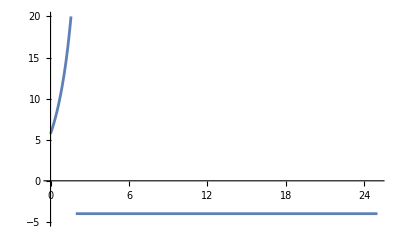

```mathematica
Plot[Evaluate[f[ai]/.constants],{ai,0,25},PlotRange->{{0,25},{-5,20}}]
```

```mathematica
subsetconstants={kPmax->1,DeltakP->1,lambda->1,Qp->10,ka->1,kQ->2}
```

{kPmax→1,DeltakP→1,lambda→1,Qp→10,ka→1,kQ→2}

```mathematica
xsols1/.subsetconstants
Solve[(avggeneric-lambda)==0,x]
```

{{x→-12/(24-40 √3)}}

```mathematica
func[x_]:=Evaluate[f[ai]/.subsetconstants]
```

```mathematica
Animate[Plot[func[x],{ai,0,25},PlotRange->{{0,2},{-5,30}}],{x,0.07747661845722373,0.999,  Appearance -> "Labeled"}]
```

```mathematica
constants
```

{kPmax→5,DeltakP→4,lambda→1,ka→4,Qp→40,kQ→1,x→13/25}

## Linear Stability Analysis

### Bimodal Equlibrium

```mathematica
expansion=Normal[Series[middadadt,{ai,abar+lambda,1}]]/.{ai->abar+lambda-δ};
expansion ==0
```

(-DeltakP kPmax^2 kQ^2-8 ka kPmax^2 lambda+DeltakP Qp^2)/(8 kPmax^2 lambda)-(DeltakP^2 Qp^2 δ)/(8 kPmax^3 lambda^2)==0

```mathematica
(* We will take the term without a delta. Need to check sign. This will allow us to state the stability since by continuity. there exist a small delta such the sign of the first term is the sign of the whole expresssion. *)
```

```mathematica
Simplify[Limit[expansion,δ->0]]
```

-ka+(DeltakP (-kPmax^2 kQ^2+Qp^2))/(8 kPmax^2 lambda)

```mathematica
(* The term seems familiar. Let's compare it to the max value of dadt.*)
```

```mathematica
maxdadt- Simplify[Limit[expansion,δ->0]]
```

0

### Zero Equilibrium

```mathematica
Simplify[middadadt+ka/.ai->abar]
```

-(DeltakP (DeltakP^2 kQ^2+4 DeltakP kPmax kQ^2+4 kPmax^2 kQ^2-4 Qp^2))/(8 (DeltakP+2 kPmax)^2 lambda)

```mathematica
Factor[DeltakP^2 kQ^2+4 DeltakP kPmax kQ^2+4 kPmax^2 kQ^2]
```

(DeltakP+2 kPmax)^2 kQ^2

```mathematica
Assuming[{DeltakP>0,lambda>0,Qp>0,kQ>0,kPmax>0},Simplify[Limit[Simplify[x/.xsols1[[1]]],ka->maxmb]]]
```

Indeterminate

```mathematica
maxmb= maxdadt+ka
```

(DeltakP (-kPmax^2 kQ^2+Qp^2))/(8 kPmax^2 lambda)

```mathematica
middadadt/.{ai->abar}
```

-((2 abar^2 DeltakP^2 (DeltakP kQ^2+8 ka lambda)-2 abar DeltakP (DeltakP+2 kPmax) lambda (DeltakP kQ^2+8 ka lambda)+2 abar DeltakP (DeltakP kQ^2+8 ka lambda) (-abar DeltakP+(DeltakP+2 kPmax) lambda)+lambda^2 (DeltakP^3 kQ^2+32 ka kPmax^2 lambda+4 DeltakP^2 (kPmax kQ^2+2 ka lambda)+4 DeltakP (kPmax^2 kQ^2+8 ka kPmax lambda-Qp^2)))/(8 (DeltakP+2 kPmax)^2 lambda^3))

(lambda (1-x))/x